## Mathematica Notebook Accompanying “Ecological memory preserves phage resistance mechanisms in bacteria”, by A. Skanata and E. Kussell

1.  Fixed point analysis

Notation:
fR - frequency of resistant cells
fS - frequency of sensitive cells
fI - frequency of infected cells
fP - frequency of phage
fA - frequency of cells that can absorb phage
(fA = fR + fS + fI for immune defenses; fA = fS + fI for preventative defenses)
Λ - growth rate
k - phage binding affinity constant; can set it to zero for high binding affinity
kL - lysing rate

```mathematica
(*definitions*)
k=0;
fP=1-fR-fS-fI;
fA=fR+fS+fI; (*specifies immune or preventative defenses*)
dkI=k+fA+fP; (*denominator in the infection rate term*)
Λ=b*fR+d*fS-kL*fI+kL*β*fI-α*fP*fA/dkI;
(*equations*)
f={(b-s-Λ)*fR,(d-α*fP/dkI)*fS+s*fR-fS*Λ,α*(fP/dkI)*fS-kL*fI-fI*Λ};
x={fR,fS,fI}; (*population vector*)
J=Simplify[Table[D[f[[i]],x[[j]]]-KroneckerDelta[i,j]*λ,{i,1,Length[f]},{j,1,Length[x]}]]; (*Jacobian matrix*)
DetJ=Simplify[Det[J]];
(*solving for fixed points*)
solfp=Solve[f==0,x];
Length[solfp]
```

8

Existence and stability of fixed points

```mathematica
solfp[[1]]
```

{fR→0,fS→0,fI→0}

```mathematica
(*E - extinction f.p. is unstable*)
```

```mathematica
{fR,fS,fI}=x/.solfp[[1]]
Solve[DetJ==0,λ]
Clear[fR,fS,fI]
```

{0,0,0}

{{λ→-kL},{λ→b-s},{λ→d-α}}

```mathematica
solfp[[2]]
```

{fR→0,fS→0,fI→(kL+α-kL β-√(-4 kL α+(-kL-α+kL β)^2))/(2 α)}

```mathematica
(*unstable*)
```

```mathematica
{fR,fS,fI}=x/.solfp[[2]]
ex=Reduce[0<fI<1&&-4 kL α+(-kL-α+kL β)^2>0&&α>0&&β>0&&kL>0,{α,β}]
solJ=Simplify[Solve[DetJ==0,λ],Assumptions->α>0&&kL>0&&β>0]
Clear[fR,fS,fI]
```

{0,0,(kL+α-kL β-√(-4 kL α+(-kL-α+kL β)^2))/(2 α)}

kL>0&&α>kL&&0<β<-2 √(α/kL)+(kL+α)/kL

{{λ→b+kL-s},{λ→1/2 (2 d+3 kL-α-kL β-√(-4 kL α+(kL+α-kL β)^2))},{λ→1/(2 α)(-kL^2 (-1+β)^2+2 kL α (1+β)-kL (-1+β) √(α^2+kL^2 (-1+β)^2-2 kL α (1+β))+α (-α+√(α^2+kL^2 (-1+β)^2-2 kL α (1+β))))}}

```mathematica
solfp[[3]]
```

{fR→0,fS→0,fI→(kL+α-kL β+√(-4 kL α+(-kL-α+kL β)^2))/(2 α)}

```mathematica
(*unstable*)
```

```mathematica
{fR,fS,fI}=x/.solfp[[3]]
Simplify[Λ]
ex=Reduce[0<fI<1&&-4 kL α+(-kL-α+kL β)^2>0&&α>0&&β>0&&kL>0,{α,β}]
solJ=Simplify[Solve[DetJ==0,λ],Assumptions->α>0&&kL>0&&β>0]
Clear[fR,fS,fI]
```

{0,0,(kL+α-kL β+√(-4 kL α+(-kL-α+kL β)^2))/(2 α)}

-kL

kL>0&&α>kL&&0<β<-2 √(α/kL)+(kL+α)/kL

{{λ→b+kL-s},{λ→1/2 (2 d+3 kL-α-kL β+√(-4 kL α+(kL+α-kL β)^2))},{λ→1/(2 α)(-kL^2 (-1+β)^2+2 kL α (1+β)+kL (-1+β) √(α^2+kL^2 (-1+β)^2-2 kL α (1+β))-α (α+√(α^2+kL^2 (-1+β)^2-2 kL α (1+β))))}}

```mathematica
solfp[[4]]
```

{fR→0,fS→1,fI→0}

```mathematica
(*S - stable for βkL<γ*)
```

```mathematica
{fR,fS,fI}=x/.solfp[[4]]
Solve[DetJ==0,λ]
Clear[fR,fS,fI]
```

{0,1,0}

{{λ→b-d-s},{λ→1/2 (-2 d-kL-α-√(kL^2-2 kL α+α^2+4 kL α β))},{λ→1/2 (-2 d-kL-α+√(kL^2-2 kL α+α^2+4 kL α β))}}

```mathematica
Solve[-2 d-kL-α+√(kL^2-2 kL α+α^2+4 kL α β)==0,β]
```

{{β→(d^2+d kL+d α+kL α)/(kL α)}}

```mathematica
γ=(d^2+d kL+d α+kL α)/α;
```

```mathematica
(*does not exist in the model*)
```

```mathematica
Simplify[solfp[[5]]]
```

{fR→-(-b+d+s)/(b-d),fS→s/(b-d),fI→0}

```mathematica
Simplify[solfp[[6]]]
```

{fR→0,fS→-((d-α) (d^2-d (α+kL (-3+β))-kL (α+kL (-2+β)-α β)))/(α (-2 d+kL (-2+β))^2),fI→-((d-α) (d^2+d (kL+α)-kL α (-1+β)))/(α (-2 d+kL (-2+β))^2)}

```mathematica
(*SP - stable for α<d & βkL between γ and γp*)
```

```mathematica
{fR,fS,fI}=x/.solfp[[6]]
Simplify[Λ]
ex=Reduce[0<fS<1&&0<fS+fI<1&&0<fI<1&&α>0&&β>0&&kL>0&&d>0,{α,β}]
solJ=Simplify[Solve[DetJ==0,λ],Assumptions->α>0&&kL>0&&β>0&&d>0]
Clear[fR,fS,fI]
```

{0,-((d-α) (d^2+3 d kL+2 kL^2-d α-kL α-d kL β-kL^2 β+kL α β))/(α (2 d+2 kL-kL β)^2),-((d-α) (d^2+d kL+d α+kL α-kL α β))/(α (2 d+2 kL-kL β)^2)}

((d-α) (d+kL-kL β))/(2 d-kL (-2+β))

kL>0&&d>0&&((0<α<d&&β>(d^2+d kL+d α+kL α)/(kL α))||(d<α≤d+2 kL&&0<β<(d^2+d kL+d α+kL α)/(kL α))||(α>d+2 kL&&(d^2+3 d kL+2 kL^2-d α-kL α)/(d kL+kL^2-kL α)<β<(d^2+d kL+d α+kL α)/(kL α)))

{{λ→1/(2 d-kL (-2+β))(-d^2+b (2 d-kL (-2+β))+d (-2 s+α+kL (-1+β))+kL (α+s (-2+β)-α β))},{λ→-1/(2 α (-2 d+kL (-2+β))^2)(d^4+2 d^3 kL+d^2 kL^2+2 d^3 α+8 d^2 kL α+10 d kL^2 α+4 kL^3 α-3 d^2 α^2-6 d kL α^2-3 kL^2 α^2-6 d^2 kL α β-10 d kL^2 α β-4 kL^3 α β+6 d kL α^2 β+6 kL^2 α^2 β+2 d kL^2 α β^2+kL^3 α β^2-2 kL^2 α^2 β^2+√(-4 (d-α) α (-2 d+kL (-2+β))^2 (d^4+d kL (-kL^2 (-2+β)+kL α (-2+β)^2+2 α^2 (-1+β))-d^3 kL (-4+β)+kL^2 α (-1+β) (α+kL (-2+β)-α β)-d^2 (α^2+kL α (-2+β)+kL^2 (-5+2 β)))+(d^4+2 d^3 (kL+α)+d^2 (kL^2-3 α^2+kL α (8-6 β))+kL^2 α (kL (-2+β)^2+α (-3+6 β-2 β^2))+2 d kL α (3 α (-1+β)+kL (5-5 β+β^2)))^2))},{λ→-1/(2 α (-2 d+kL (-2+β))^2)(d^4+2 d^3 kL+d^2 kL^2+2 d^3 α+8 d^2 kL α+10 d kL^2 α+4 kL^3 α-3 d^2 α^2-6 d kL α^2-3 kL^2 α^2-6 d^2 kL α β-10 d kL^2 α β-4 kL^3 α β+6 d kL α^2 β+6 kL^2 α^2 β+2 d kL^2 α β^2+kL^3 α β^2-2 kL^2 α^2 β^2-√(-4 (d-α) α (-2 d+kL (-2+β))^2 (d^4+d kL (-kL^2 (-2+β)+kL α (-2+β)^2+2 α^2 (-1+β))-d^3 kL (-4+β)+kL^2 α (-1+β) (α+kL (-2+β)-α β)-d^2 (α^2+kL α (-2+β)+kL^2 (-5+2 β)))+(d^4+2 d^3 (kL+α)+d^2 (kL^2-3 α^2+kL α (8-6 β))+kL^2 α (kL (-2+β)^2+α (-3+6 β-2 β^2))+2 d kL α (3 α (-1+β)+kL (5-5 β+β^2)))^2))}}

```mathematica
st1=Reduce[1/(2 d-kL (-2+β))(-d^2+b (2 d-kL (-2+β))+d (-2 s+α+kL (-1+β))+kL (α+s (-2+β)-α β))<0&&ex&&d>b>s>0,{α,β}]
```

s>0&&b>s&&d>b&&kL>0&&((0<α≤-b+d+s&&β>(d^2+d kL+d α+kL α)/(kL α))||(-b+d+s<α<d&&(d^2+d kL+d α+kL α)/(kL α)<β<(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b kL-d kL-kL s+kL α))||(α>d&&(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b kL-d kL-kL s+kL α)<β<(d^2+d kL+d α+kL α)/(kL α)))

```mathematica
γp=(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b-d -s+ α);
```

```mathematica
(*all eigenvalues are real*)
```

```mathematica
Simplify[solJ[[2]][[1]][[2]]-solJ[[3]][[1]][[2]]]
```

-1/(α (-2 d+kL (-2+β))^2)(√(-4 (d-α) α (-2 d+kL (-2+β))^2 (d^4+d kL (-kL^2 (-2+β)+kL α (-2+β)^2+2 α^2 (-1+β))-d^3 kL (-4+β)+kL^2 α (-1+β) (α+kL (-2+β)-α β)-d^2 (α^2+kL α (-2+β)+kL^2 (-5+2 β)))+(d^4+2 d^3 (kL+α)+d^2 (kL^2-3 α^2+kL α (8-6 β))+kL^2 α (kL (-2+β)^2+α (-3+6 β-2 β^2))+2 d kL α (3 α (-1+β)+kL (5-5 β+β^2)))^2))

```mathematica
Reduce[(-4 (d-α) α (-2 d+kL (-2+β))^2 (d^4+d kL (-kL^2 (-2+β)+kL α (-2+β)^2+2 α^2 (-1+β))-d^3 kL (-4+β)+kL^2 α (-1+β) (α+kL (-2+β)-α β)-d^2 (α^2+kL α (-2+β)+kL^2 (-5+2 β)))+(d^4+2 d^3 (kL+α)+d^2 (kL^2-3 α^2+kL α (8-6 β))+kL^2 α (kL (-2+β)^2+α (-3+6 β-2 β^2))+2 d kL α (3 α (-1+β)+kL (5-5 β+β^2)))^2)<0&&ex]
```

False

```mathematica
(*unstable for α>d*)
```

```mathematica
Reduce[solJ[[3]][[1]][[2]]<0&&ex]
```

α>0&&d>α&&kL>0&&β>(d^2+d kL+d α+kL α)/(kL α)

```mathematica
(*the remaining two solutions correspond to the RSP fixed point*)
```

```mathematica
(*checking where the solutions become unstable*)
```

```mathematica
a0=Normal[Series[-DetJ,{λ,0,0}]];
a1=(Normal[Series[-DetJ,{λ,0,1}]]-a0)/λ;
a2=(Normal[Series[-DetJ,{λ,0,2}]]-a1*λ-a0)/λ^2;
Eq=Simplify[a1*a2-a0];
```

{(b^2 s+36+(b kL α β 1^2)/(4 1^2)-(d kL α β (1)^2)/(4 (1-1)^2))/(-b^2 s+b d s-b kL s+d kL s+b s^2-d s^2-b s α-kL s α),1/(2 1),(-b^2 s-b kL s+22+(d 3 1^2)/(4 1^2))/(b^3-b^2 d+2 b^2 kL-2 b d kL+13+2 b kL α+kL^2 α-b s α-kL s α)}
 |  |  |  |

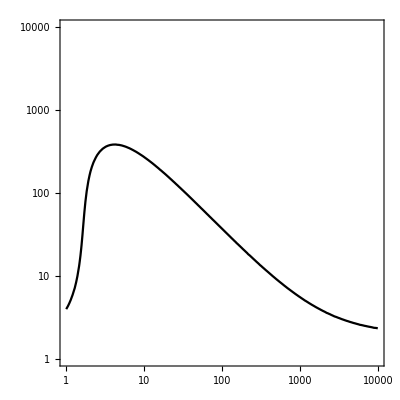

```mathematica
{fR,fS,fI}=x/.solfp[[7]]
b=0.9;d=1;kL=1;s=0.0001;
γpp=ContourPlot[Eq==0,{α,1,10000},{β,1,10000},ContourStyle->Black,ScalingFunctions->{"Log","Log"}]
Clear[fR,fS,fI]
Clear[b,d,kL,s]
```

```mathematica
{fR,fS,fI}=x/.solfp[[8]]
b=0.9;d=1;kL=1;s=0.0001;
ContourPlot[Eq==0,{α,1,10000},{β,1,10000},ContourStyle->{Black,Thickness[0.01]},ScalingFunctions->{"Log","Log"}]
Clear[fR,fS,fI]
Clear[b,d,kL,s]
```

{(b^2 s+36+(b kL α β 1^2)/(4 1^2)-(d kL α β (1)^2)/(4 (1-1)^2))/(-b^2 s+b d s-b kL s+d kL s+b s^2-d s^2-b s α-kL s α),1/(2 1),(-b^2 s-b kL s+22+(d 3 1^2)/(4 1^2))/(b^3-b^2 d+2 b^2 kL-2 b d kL+13+2 b kL α+kL^2 α-b s α-kL s α)}
 |  |  |  |

-Graphics-

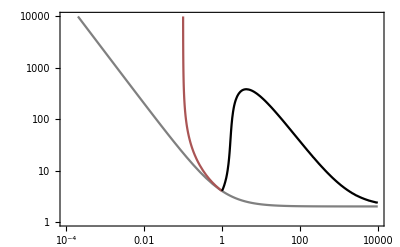

```mathematica
b=0.9;d=1;kL=1;s=0.0001;
pl0=LogLogPlot[γ,{α,0.0001,10000},PlotRange->{1,10000},Frame->True,PlotStyle->Gray];
pl1=LogLogPlot[γp,{α,0.0001,1},PlotRange->{1,10000},Frame->True,PlotStyle->Darker[Pink]];
Show[pl0,pl1,γpp]
Clear[b,d,kL,s]
```

2.  Flow diagrams

```mathematica
trianglemap[{X_,Z_}]:={X+Z*Cos[Pi/3],Z *Sin[Pi/3]};
```

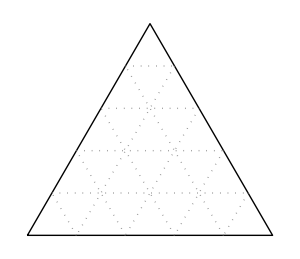

```mathematica
cl=Graphics[{Line[{{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}}]},ImageSize->300];

rl=Graphics[Table[{Dotted,Gray,Line[{{i √3/2 Tan[30 Degree],i √3/2},{1-i √3/2Tan[30 Degree],i √3/2}}]},{i,0.2,0.9,0.2}],ImageSize->300];
rlt=Graphics[Table[{Black,Line[{{1-i √3/2Tan[30 Degree],i √3/2},{0.02+1-i √3/2Tan[30 Degree],i √3/2}}]},{i,0,1,0.2}],ImageSize->300];
bl=Graphics[Table[{Dotted,Gray,Rotate[Line[{{0+i √3/2 Tan[30 Degree],i √3/2},{1-i √3/2Tan[30 Degree],i √3/2}}],120 Degree,{0.5,√3/6}]},{i,0.2,0.9,0.2}],ImageSize->300];
blt=Graphics[Table[{Black,Rotate[Line[{{1-i √3/2 Tan[30 Degree],i √3/2},{0.02+1-i √3/2 Tan[30 Degree],i √3/2}}],120 Degree,{0.5,√3/6}]},{i,0,1,0.2}],ImageSize->300];
gl=Graphics[Table[{Dotted,Gray,Rotate[Line[{{0+i √3/2 Tan[30 Degree],i √3/2},{1-i √3/2Tan[30 Degree],i √3/2}}],-120 Degree,{0.5,√3/6}]},{i,0.2,0.9,0.2}],ImageSize->300];
glt=Graphics[Table[{Black,Rotate[Line[{{0.02+1-i √3/2 Tan[30 Degree],i √3/2},{1-i √3/2Tan[30 Degree],i √3/2}}],-120 Degree,{0.5,√3/6}]},{i,0,1,0.2}],ImageSize->300];
tpl=Show[cl,rl,bl,gl]
```

```mathematica
λ[fR_,fS_,fI_]:=b*fR+d*fS+kL*fI*(β-1)-α*(1-fR-fS-fI)*(fR+fS+fI)/(1-fR);
```

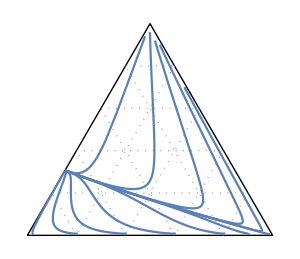

```mathematica
initpts={{0.2,0.79,0.},{0.4,0.59,0.},{0.6,0.39,0.},{0.8,0.19,0.},{0.02,0.97,0.},{0.9,0.09,0.},{0.98,0.01,0.},{0.02,0.02,0.},{0.09,0.01,0.},{0.29,0.01,0.},{0.06,0.02,0.},{0.01,0.05,0.}};

d=1;kL=1;β=20.;α=0.15;b=0.9;s=0.0001;

tmax=100;
pts={};
arrowpts={};
Do[
fRi=initpts[[k]][[1]];
fSi=initpts[[k]][[2]];
fIi=initpts[[k]][[3]];
sol=NDSolve[{fR'[t]==(b-s-λ[fR[t],fS[t],fI[t]])*fR[t],fS'[t]==(d-λ[fR[t],fS[t],fI[t]]-α*(1-fR[t]-fS[t]-fI[t])/(1-fR[t]))*fS[t]+s*fR[t],fI'[t]==-kL*fI[t]-λ[fR[t],fS[t],fI[t]]*fI[t]+fS[t]*α*(1-fR[t]-fS[t]-fI[t])/(1-fR[t]),fR[0]==fRi,fS[0]==fSi,fI[0]==fIi},{fR,fS,fI},{t,0,tmax}];
tg=ParametricPlot[trianglemap[{sol[[1]][[1]][[2]][t],1-sol[[1]][[1]][[2]][t]-sol[[1]][[2]][[2]][t]}],{t,0,tmax}];
apts=Table[trianglemap[{sol[[1]][[1]][[2]][t],1-sol[[1]][[1]][[2]][t]-sol[[1]][[2]][[2]][t]}],{t,{tmax-10,tmax}}];
AppendTo[arrowpts,apts];
AppendTo[pts,tg],{k,1,Length[initpts]}];
Clear[d,αL,β,α,b,s]
plts=Show[pts];

arrows=Show[Table[Graphics[Arrow[arrowpts[[i]]]],{i,1,Length[arrowpts]}]];
Show[tpl,plts,ImageSize->300]
```

3.  Single patch invasion dynamics

```mathematica
(*preventative defenses -- for immune defenses check Julia notebook*)
```

```mathematica
(*in turbidostat coordinates*)
(*X and Y are the frequencies of the resistant, and sensitive phenotype in the resistance switching strain, X0 is the resistant phenotype of the non-switching strain, Y0 is the sensitive phenotype of the S strain*)
```

```mathematica
L[X0_,X_,Y_,Y0_]:=b*(X0+X)+d*(Y+Y0)-kL*(1-X0-X-Y0-Y);(*long term growth rate*)
```

```mathematica
(*parameters*)
d=1.;b=0.9;kL=1.;s=0.001;α=10.;β=50.;
```

```mathematica
(*invading S with Rs*)
```

```mathematica
(*Rs fixed point*)
```

```mathematica
Rsfp=NSolve[{0==(b-s-L[0,X,Y,0])*X,0==(d-L[0,X,Y,0])*Y+s*X-α*Y*p/(1-X+p),0==kL*β*(1-X-Y)-L[0,X,Y,0]*p-α*p/(1-X+p)},{X,Y,p}]
```

{{X→0.,Y→0.,p→-39.7419},{X→0.,Y→-4.19565,p→-26.5556},{X→0.999367,Y→0.000100951,p→-11.0945},{X→0.,Y→0.,p→-1.25812},{X→1.01,Y→-0.01,p→0.},{X→0.959347,Y→0.0381206,p→0.00051946},{X→0.,Y→1.,p→0.}}

```mathematica
{Xs,Ys,ps}={X,Y,p}/.Rsfp[[6]]
```

{0.959347,0.0381206,0.00051946}

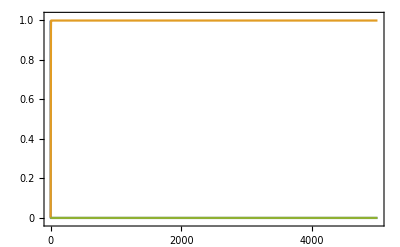

{4.33619×10^-42,0.999364,0.000103813,0.0226988}

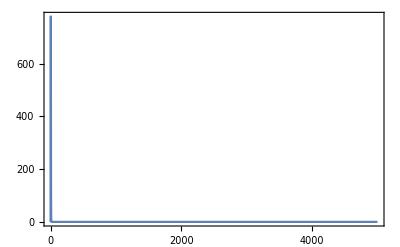

```mathematica
f=0.001;(*initial frequency of invading strains*)
tmax=5000;
Xi=f*Xs;
Yi=f*Ys;
pi=f*ps;
Y0i=1-f;

sol=NDSolve[{Y0'[t]==(d-L[0,X[t],Y[t],Y0[t]])*Y0[t]-α*Y0[t]*p[t]/(1-X[t]+p[t]),X'[t]==(b-s-L[0,X[t],Y[t],Y0[t]])*X[t],Y'[t]==(d-L[0,X[t],Y[t],Y0[t]])*Y[t]+s*X[t]-α*Y[t]*p[t]/(1-X[t]+p[t]),p'[t]==kL*β*(1-X[t]-Y[t]-Y0[t])-L[0,X[t],Y[t],Y0[t]]*p[t]-α*p[t]*(1-X[t])/(1-X[t]+p[t]),Y0[0]==Y0i,X[0]==Xi,Y[0]==Yi,p[0]==pi},{Y0,X,Y,p},{t,0,tmax}];
Plot[{sol[[1]][[1]][[2]][t],sol[[1]][[2]][[2]][t],sol[[1]][[3]][[2]][t]},{t,0,tmax},PlotRange->{-0.02,1.02},Frame->True,FrameTicks->All]
Table[sol[[1]][[i]][[2]][tmax],{i,1,4}]
Plot[sol[[1]][[4]][[2]][t],{t,0,tmax},PlotRange->All,Frame->True,FrameTicks->All]
```

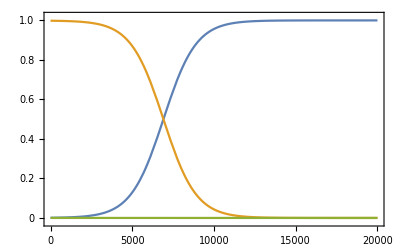

Part::partw: Part 5 of {«1»} does not exist.

{0.999998,2.06589×10^-6,2.14128×10^-10,4.80852×10^-8,5[20000]}

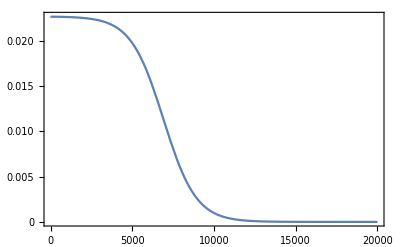

```mathematica
X0i=f;
Xi=sol[[1]][[2]][[2]][tmax]*(1-f);
Yi=sol[[1]][[3]][[2]][tmax]*(1-f);
pi=sol[[1]][[4]][[2]][tmax];
tmax2=20000;

sol2=NDSolve[{X0'[t]==(b-L[X0[t],X[t],Y[t],0])*X0[t],X'[t]==(b-s-L[X0[t],X[t],Y[t],0])*X[t],Y'[t]==(d-L[X0[t],X[t],Y[t],0])*Y[t]+s*X[t]-α*Y[t]*p[t]/(1-X[t]-X0[t]+p[t]),p'[t]==kL*β*(1-X[t]-Y[t]-X0[t])-L[X0[t],X[t],Y[t],0]*p[t]-α*p[t](1-X[t]-X0[t])/(1-X[t]-X0[t]+p[t]),X0[0]==X0i,X[0]==Xi,Y[0]==Yi,p[0]==pi},{X0,X,Y,p},{t,0,tmax2}];
Plot[{sol2[[1]][[1]][[2]][t],sol2[[1]][[2]][[2]][t],sol2[[1]][[3]][[2]][t]},{t,0,tmax2},PlotRange->{-0.02,1.02},Frame->True,FrameTicks->All]
Table[sol2[[1]][[i]][[2]][tmax2],{i,1,5}]
Plot[sol2[[1]][[4]][[2]][t],{t,0,tmax2},PlotRange->All,Frame->True,FrameTicks->All]
```

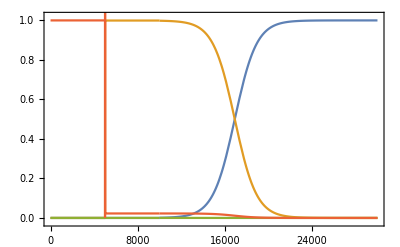

```mathematica
tS=tmax;plotbox=Plot[-0.05,{t,0,tS+tmax+tmax2},PlotRange->{-0.02,1.02},Frame->True,FrameTicks->None];
plotS=Plot[{0,0,0,1.},{t,0,tmax}];
plotRs=Plot[{0,sol[[1]][[2]][[2]][t-tS],sol[[1]][[3]][[2]][t-tS],sol[[1]][[4]][[2]][t-tS]},{t,tS,tS+tmax},PlotRange->All];
plotR0=Plot[{sol2[[1]][[1]][[2]][t-tS-tmax],sol2[[1]][[2]][[2]][t-tS-tmax],sol2[[1]][[3]][[2]][t-tS-tmax],sol2[[1]][[4]][[2]][t-tS-tmax]},{t,tS+tmax,tS+tmax+tmax2},PlotRange->All];
Show[plotbox,plotS,plotRs,plotR0]
```

4.  Chemostat control

```mathematica
(*preventative*)
(*r = resource*)
```

```mathematica
b[r_]:=b0*r;
d[r_]:=d0*r;
k=0;
eqs={-b[r]*R-d[r]*S+DR*(rin-r),b[r]*R-s*R-DR*R,d[r]*S-DR*S+s*R-α*P*S/(k+P+S+L),-kL*L-DR*L+α*P*S/(k+P+S+L),kL*β*L-DR*P-α*P*(S+L)/(k+P+S+L)};
vars={r,R,S,L,P};
J=Simplify[Table[D[eqs[[i]],vars[[j]]]-KroneckerDelta[i,j]*λ,{i,1,Length[eqs]},{j,1,Length[vars]}]];
sols=Simplify[Solve[eqs==0,vars]];
Length[sols]
solfp=Table[vars/.sols[[i]],{i,1,Length[sols]}];
solfp[[1]]
```

6

{DR/d0,0,-DR/d0+rin,0,0}

```mathematica
betavals=Table[Exp[i],{i,-2.3,6.9,0.05}];
alphavals=Table[Exp[i],{i,-6.9,4.6,0.05}];
Length[alphavals]*Length[betavals]
```

42735

```mathematica
b0=0.9;d0=1.;DR=0.4;rin=1.;kL=1.;
s=0.0001;
```

20165

4406

18154

10

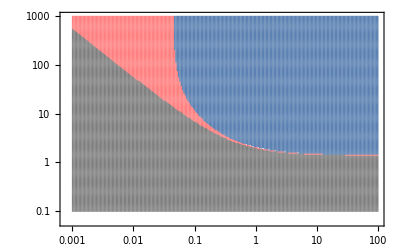

```mathematica
SetSharedVariable[RSPphase,SPphase,Sphase]
RSPphase={};
SPphase={};
Sphase={};

Monitor[ParallelDo[
α=alphavals[[ai]];
Do[
β=betavals[[bi]];
Do[
r=solfp[[i]][[1]];
R=solfp[[i]][[2]];
S=solfp[[i]][[3]];
L=solfp[[i]][[4]];
P=solfp[[i]][[5]];
test=0;
If[Element[R,Reals]&&Element[S,Reals]&&Element[L,Reals]&&Element[P,Reals]&&r>0.&&R≥0.&&S>0.&&L≥0.&&P≥0.,
solL=NSolve[Det[J]==0,λ];
If[Sum[Sign[Re[solL[[j]][[1]][[2]]]],{j,1,5}]==-5,test=1]];
If[test==1,
If[R>0.,AppendTo[RSPphase,{α,β}],If[P>0.,AppendTo[SPphase,{α,β}],AppendTo[Sphase,{α,β}]]]];
Clear[r,R,S,P,L],{i,1,6}],{bi,1,Length[betavals]}],{ai,1,Length[alphavals]}],{Length[Sphase],Length[SPphase],Length[RSPphase]}];
Length[Sphase]
Length[SPphase]
Length[RSPphase]
unst=Length[alphavals]*Length[betavals]-Length[Sphase]-Length[SPphase]-Length[RSPphase]
prevplot=ListPlot[{Sphase,SPphase,RSPphase},ScalingFunctions->{"Log","Log"},Frame->True,PlotStyle->{Gray,Pink,RGBColor[0.36,0.51,0.7]}]
```

```mathematica
(*for immune defenses use*)
eqs={-b[r]*R-d[r]*S+DR*(rin-r),b[r]*R-s*R-DR*R,d[r]*S-DR*S+s*R-α*P*S/(k+P+S+L+R),-αL*L-DR*L+α*P*S/(k+P+S+L+R),αL*β*L-DR*P-α*P*(S+L+R)/(k+P+S+L+R)};
(*for L-V interactions use (η=0 for preventative, η=1 for immune)*)
eqs={-b[r]*R-d[r]*S+DR*(rin-r),b[r]*R-s*R-DR*R,d[r]*S-DR*S+s*R-α*P*S,-αL*L-DR*L+α*P*S,αL*β*L-DR*P-α*P*(S+L+η*R)};
```

5.  CRISPR  spacer loss model

```mathematica
(*turbidostat control*)
```

```mathematica
(*X = frequency of resistant, Y = frequency of sensitive, T = frequency of invader*)
```

```mathematica
Λ=b*(X+Y)+d*T-kL*(1-X-Y-T);
f={(b-s-Λ)*X,(b-α*(p/(1+p)))*Y+s*X-Y*Λ,(d-α*(p/(1+p)))*T-T*Λ,-α*(p/(1+p))+kL*β*(1-X-Y-T)-p*Λ};
x={X,Y,T,p};
J=Table[D[f[[i]],x[[j]]]-KroneckerDelta[i,j]*λ,{i,1,Length[f]},{j,1,Length[x]}];
DetJ=Simplify[Det[J]];
solfp=Simplify[Solve[f==0,x]];
Length[solfp]
```

9

```mathematica
(*stability analysis*)
```

```mathematica
solfp[[1]]
```

{X→0,Y→0,T→1,p→0}

```mathematica
(*T fixed point stable for βkL<γ*)
```

```mathematica
{X,Y,T,p}=x/.solfp[[1]]
Solve[DetJ==0,λ]
Clear[X,Y,T,p]
```

{0,0,1,0}

{{λ→b-d},{λ→b-d-s},{λ→1/2 (-2 d-kL-α-√(kL^2-2 kL α+α^2+4 kL α β))},{λ→1/2 (-2 d-kL-α+√(kL^2-2 kL α+α^2+4 kL α β))}}

```mathematica
Solve[-2 d-kL-α+√(kL^2-2 kL α+α^2+4 kL α β)==0,β]
```

{{β→(d^2+d kL+d α+kL α)/(kL α)}}

```mathematica
γ=(d^2+d kL+d α+kL α)/α;
```

```mathematica
solfp[[2]]
```

{X→0,Y→1,T→0,p→0}

```mathematica
(*S is unstable*)
```

```mathematica
{X,Y,T,p}=x/.solfp[[2]]
Solve[DetJ==0,λ]
Clear[X,Y,T,p]
```

{0,1,0,0}

{{λ→-b+d},{λ→-s},{λ→1/2 (-2 b-kL-α-√(kL^2-2 kL α+α^2+4 kL α β))},{λ→1/2 (-2 b-kL-α+√(kL^2-2 kL α+α^2+4 kL α β))}}

```mathematica
solfp[[3]]
```

{X→(d^2+b (-2 d+kL (-2+β))+d (kL+2 s-α-kL β)-kL (α+s (-2+β)-α β))/(kL (b-d-s+α) β),Y→(s (-d^2+b (2 d-kL (-2+β))+d (-2 s+α+kL (-1+β))+kL (α+s (-2+β)-α β)))/((b-d) kL (b-d-s+α) β),T→(2 b^3+b^2 (-3 d+2 kL-4 s+α)+b (d^2+s (2 s-α)-d (3 kL-3 s+α)+kL (α+s (-4+β)))+kL (d^2-d (α+s (-3+β))-s (α+s (-2+β)-α β)))/((b-d) kL (b-d-s+α) β),p→(-b+d+s)/(b-d-s+α)}

```mathematica
(*S'RSP phase*)
```

```mathematica
{X,Y,T,p}=x/.solfp[[3]]
ex=Reduce[0<X<1&&0<Y<1&&0<T<1&&0<X+Y+T<1&&p>0&&d>b>s>0&&α>0&&β>0&&kL>0,{α,β}]
Clear[X,Y,T,p]
```

{(d^2+b (-2 d+kL (-2+β))+d (kL+2 s-α-kL β)-kL (α+s (-2+β)-α β))/(kL (b-d-s+α) β),(s (-d^2+b (2 d-kL (-2+β))+d (-2 s+α+kL (-1+β))+kL (α+s (-2+β)-α β)))/((b-d) kL (b-d-s+α) β),(2 b^3+b^2 (-3 d+2 kL-4 s+α)+b (d^2+s (2 s-α)-d (3 kL-3 s+α)+kL (α+s (-4+β)))+kL (d^2-d (α+s (-3+β))-s (α+s (-2+β)-α β)))/((b-d) kL (b-d-s+α) β),(-b+d+s)/(b-d-s+α)}

s>0&&b>s&&d>b&&kL>0&&α>-b+d+s&&(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b kL-d kL-kL s+kL α)<β<(-2 b^3+3 b^2 d-b d^2-2 b^2 kL+3 b d kL-d^2 kL+4 b^2 s-3 b d s+4 b kL s-3 d kL s-2 b s^2-2 kL s^2-b^2 α+b d α-b kL α+d kL α+b s α+kL s α)/(b kL s-d kL s-kL s^2+kL s α)

```mathematica
γp=(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b-d -s+ α);
γppp=(-2 b^3+3 b^2 d-b d^2-2 b^2 kL+3 b d kL-d^2 kL+4 b^2 s-3 b d s+4 b kL s-3 d kL s-2 b s^2-2 kL s^2-b^2 α+b d α-b kL α+d kL α+b s α+kL s α)/(b s-d s- s^2+ s α);
```

```mathematica
a4=Simplify[(Normal[Series[DetJ,{λ,0,4}]]-Normal[Series[DetJ,{λ,0,3}]])/λ^4]
a3=Simplify[(Normal[Series[DetJ,{λ,0,3}]]-Normal[Series[DetJ,{λ,0,2}]])/λ^3];
a2=Simplify[(Normal[Series[DetJ,{λ,0,2}]]-Normal[Series[DetJ,{λ,0,1}]])/λ^2];
a1=Simplify[(Normal[Series[DetJ,{λ,0,1}]]-Normal[Series[DetJ,{λ,0,0}]])/λ];
a0=Simplify[Normal[Series[DetJ,{λ,0,0}]]];
Eq=Simplify[a1*(a2*a3-a1)-a0*a3*a3];
```

1

{(d^2+b (-2 d+kL (-2+β))+d (kL+2 s-α-kL β)-kL (α+s (-2+β)-α β))/(kL (b-d-s+α) β),(s (-d^2+b (2 d-kL (-2+β))+d (-2 s+α+kL (-1+β))+kL (α+s (-2+β)-α β)))/((b-d) kL (b-d-s+α) β),1/((b-d) kL (b-d-s+α) β)(2 b^3+b^2 (-3 d+2 kL-4 s+α)+b (d^2+s (2 s-α)-d (3 kL-3 s+α)+kL (α+s (-4+β)))+kL (d^2-d (α+s (-3+β))-s (α+s (-2+β)-α β))),(-b+d+s)/(b-d-s+α)}

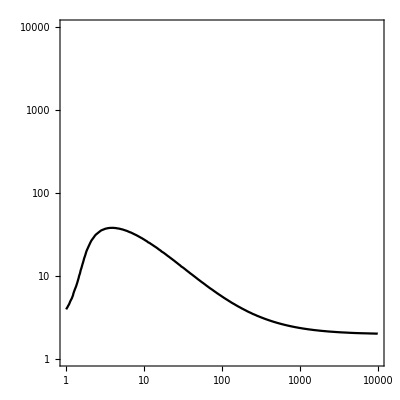

```mathematica
{X,Y,T,p}=x/.solfp[[3]]
b=0.9;d=1;kL=1;s=0.001;
γpp=ContourPlot[Eq==0,{α,1,10000},{β,1,10000},ContourStyle->Black,ScalingFunctions->{"Log","Log"},RegionFunction->Function[{α,β},β>(d+α)*(d+kL)/(α*kL)]]
Clear[X,Y,T,p]
Clear[b,d,kL,s]
```

```mathematica
solfp[[4]]
```

{X→0,Y→(b^2-b (α+kL (-3+β))-kL (α+kL (-2+β)-α β))/((b+kL) (2 b-kL (-2+β))),T→0,p→-(b^2+b (kL+α)-kL α (-1+β))/((b+kL) (b-α))}

```mathematica
(*SP is unstable*)
```

```mathematica
{X,Y,T,p}=x/.solfp[[4]]
solJ=Solve[DetJ==0,λ];
solJ[[1]]
Clear[X,Y,T,p]
```

{0,(b^2-b (α+kL (-3+β))-kL (α+kL (-2+β)-α β))/((b+kL) (2 b-kL (-2+β))),0,-(b^2+b (kL+α)-kL α (-1+β))/((b+kL) (b-α))}

{λ→-b+d}

```mathematica
(*This is the TP phase, which is stable for γ<βkL<γp and α<d*)
```

```mathematica
solfp[[5]]
```

{X→0,Y→0,T→(d^2-d (α+kL (-3+β))-kL (α+kL (-2+β)-α β))/((d+kL) (2 d-kL (-2+β))),p→-(d^2+d (kL+α)-kL α (-1+β))/((d+kL) (d-α))}

```mathematica
γp=(2 b d-d^2+2 b kL-d kL-2 d s-2 kL s+d α+kL α)/(b-d -s+ α);
```

```mathematica
(*these are unstable*)
```

```mathematica
solfp[[6]]
solfp[[7]]
```

{X→0,Y→0,T→0,p→-(kL-α+kL β+√(-4 kL^2 β+(kL-α+kL β)^2))/(2 kL)}

{X→0,Y→0,T→0,p→(-kL+α-kL β+√(-4 kL^2 β+(kL-α+kL β)^2))/(2 kL)}

```mathematica
(*these are the solutions corresponding to the RSP phase, which exists and is stable for βkL>γppp*)
```

```mathematica
solfp[[8]]
solfp[[9]]
```

{X→-1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-2 kL α β-√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),Y→1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),T→0,p→-1/(2 (b+kL) (b-s))(b^2+b kL-b s-kL s+b α+kL α-kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2))}

{X→-1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-2 kL α β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),Y→1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),T→0,p→1/(2 (b+kL) (b-s))(-b^2-b kL+b s+kL s-b α-kL α+kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2))}

```mathematica
{X,Y,T,p}=x/.solfp[[8]]
ex=Reduce[0<X<1&&0<Y<1&&0<X+Y<1&&p>0&&d>b>s>0&&α>0&&β>0&&kL>0,{α,β}]
Clear[X,Y,T,p]
```

{-1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-2 kL α β-√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),0,-(b^2+b kL-b s-kL s+b α+kL α-kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2))/(2 (b+kL) (b-s))}

False

```mathematica
{X,Y,T,p}=x/.solfp[[9]]
ex=Reduce[0<X<1&&0<Y<1&&0<X+Y<1&&p>0&&d>b>s>0&&α>0&&β>0&&kL>0,{α,β}]
Clear[X,Y,T,p]
```

{-1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β-2 kL α β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),1/(2 kL (b+kL) α β)(b+kL-s) (b^2+b kL-b s-kL s+b α+kL α+kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2)),0,(-b^2-b kL+b s+kL s-b α-kL α+kL s β+√(4 kL (b+kL) (b-s) s β+(b^2+b (kL-s+α)-kL (s-α+s β))^2))/(2 (b+kL) (b-s))}

s>0&&b>s&&kL>0&&d>b&&α>s&&β>(-b^2-b kL+2 b s+2 kL s-b α-kL α)/(kL s-kL α)

```mathematica
T=0;
solJ=Solve[Simplify[DetJ]==0,λ];
Clear[T]
```

```mathematica
{X,Y,T,p}=x/.solfp[[9]];
Reduce[ex&&solJ[[1]][[1]][[2]]<0,{α,β}]
Clear[X,Y,T,p]
```

s>0&&b>s&&d>b&&kL>0&&α>-b+d+s&&β>(-2 b^3+3 b^2 d-b d^2-2 b^2 kL+3 b d kL-d^2 kL+4 b^2 s-3 b d s+4 b kL s-3 d kL s-2 b s^2-2 kL s^2-b^2 α+b d α-b kL α+d kL α+b s α+kL s α)/(b kL s-d kL s-kL s^2+kL s α)

```mathematica
(*phase plot*)
```

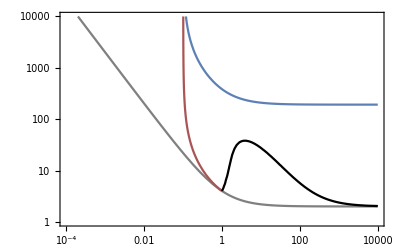

```mathematica
b=0.9;d=1;kL=1;s=0.001;
pl0=LogLogPlot[γ,{α,0.0001,10000},PlotRange->{1,10000},Frame->True,PlotStyle->Gray];
pl1=LogLogPlot[γp,{α,0.0001,1},PlotRange->{1,10000},Frame->True,PlotStyle->Darker[Pink]];
pl3=LogLogPlot[γppp,{α,0.0001,10000},PlotRange->{1,10000},Frame->True];
Show[pl0,pl1,γpp,pl3]
Clear[b,d,kL,s]
```

6.  Game theory flows

```mathematica
(*x1 == Rs strategy, x2 = R0 strategy, x3 = S strategy*)
(*r = (s-c)/(s+c)*)
```

```mathematica
x={x1,x2,x3};
mat={{0,-1,1},{r,0,-1},{-1,1,0}};
mat//MatrixForm
matx=mat.x
ϕ=x.mat.x
f=Simplify[Table[x[[i]]*(-ϕ+matx[[i]]),{i,1,Length[x]}]]
```

(0 | -1 | 1
r | 0 | -1
-1 | 1 | 0)

{-x2+x3,r x1-x3,-x1+x2}

x1 (r x2-x3)+(x1-x2) x3+x2 (-x1+x3)

{-x1 (x2+(-1+r) x1 x2-x3),-x2 (r x1 (-1+x2)-x1 x2+x3),-(x1-x2+(-1+r) x1 x2) x3}

```mathematica
x3=1-x1-x2;
ft=f/.x1->x1[t]/.x2->x2[t];
```

```mathematica
x1i=1/3;
x2i=1/3;r=0.2;
tmax=100;solRPS=NDSolve[{x1'[t]==ft[[1]],x2'[t]==ft[[2]],x1[0]==x1i,x2[0]==x2i},{x1,x2},{t,0,tmax}]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

```mathematica
trianglemap[{X_,Z_}]:={X+Z*Cos[Pi/3],Z *Sin[Pi/3]};
cl=Graphics[{Line[{{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}}]},ImageSize->300];
```

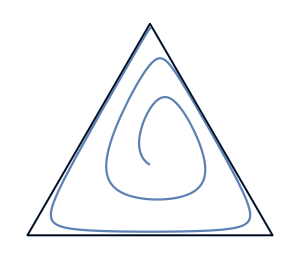

```mathematica
plRPs=Show[cl,ParametricPlot[trianglemap[{solRPS[[1]][[2]][[2]][t],solRPS[[1]][[1]][[2]][t]}],{t,0,tmax}],cl]
```

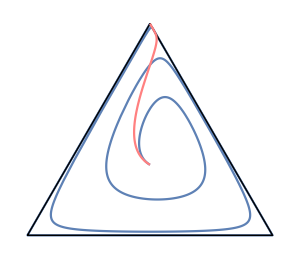

```mathematica
x1i=1/3;
x2i=1/3;r=-0.2;
tmax=100;solRPS2=NDSolve[{x1'[t]==ft[[1]],x2'[t]==ft[[2]],x1[0]==x1i,x2[0]==x2i},{x1,x2},{t,0,tmax}];
Show[plRPs,ParametricPlot[trianglemap[{solRPS2[[1]][[2]][[2]][t],solRPS2[[1]][[1]][[2]][t]}],{t,0,tmax},PlotStyle->Pink]]
```